# wtf yo

```mathematica
Clear["Global`*"]
ns=10^-9;
ms=10^-3;
MHz=10^6;
μB=9.274009994 10^-24;
G=10^-4;
ℏ=1.0545718 10^-34;
kHz=10^3;
Ω=2π 1/(8 .01 ms);

Δ=.35MHz;100Ω;
B0=ℏ/μB Δ;

Bx[t_]:=0;
By[t_]:=B0 Sin[Ω t];
Bz[t_]:=B0 Cos[Ω t];


H[t_]:=μB/2(PauliMatrix[1]Bx[t]+PauliMatrix[2]By[t]+PauliMatrix[3]Bz[t]);
```

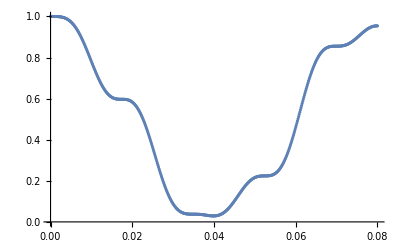

```mathematica
Ψ0=Transpose[{{1,0}}];
Ψk=Ψ0;
Δt=.05/Δ;
list=Reap[Do[
k1=-I/ℏ H[t].Ψk;
k2 =-I/ℏ H[t+Δt/2].(Ψk+Δt/2 k1);
k3 =-I/ℏ H[t+Δt/2].(Ψk+Δt/2 k2);
k4 =-I/ℏ H[t+Δt].(Ψk+Δt k3);
Ψk=Ψk+ Δt/6(k1+2k2+2k3+k4);

Sow[{t/ms,Abs[Ψk[[1,1]]]^2,Abs[Ψk[[2,1]]]^2,Ψk}];
,{t,0,(2π)/Ω,Δt}]][[2,1]];

ListPlot[list[[;;,{1,2}]]]
```

```mathematica
(*transform to bloch vector*)
T=.1;
Ψk=Cases[list,x_/;T-Δt/ms≤ x[[1]]≤ T][[-1,-1]];
u=2 Re[Ψk[[1,1]]Ψk[[2,1]]*];
v=2 Im[Ψk[[1,1]]*Ψk[[2,1]]];
w=Abs[Ψk[[1,1]]]^2-Abs[Ψk[[2,1]]]^2;
BV=Transpose[{{u,v,w}}]
Rx[θ_]:={{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}};
{u,v,w}=Transpose[Rx[45 π/180].BV][[1]];

a=√((u^2+v^2)/(2(1-w)));
B=√((1-w)/2);
NSolve[{Cos[θ]==u/(2 a B)&&Sin[θ]==-v/(2 a B)},θ]
bb=-.0122;

u/(2a B)
Cos[bb]
-v/(2a B)
Sin[bb]
```

{{0.019997},{0.707137},{0.706794}}

{}

0.999926

0.999926

-0.0121466

-0.0121997

# backup; resonant drive

```mathematica
Clear["Global`*"]
ns=10^-9;
ms=10^-3;
MHz=10^6;
μB=9.274009994 10^-24;
G=10^-4;
ℏ=1.0545718 10^-34;
kHz=10^3;
Ω=2π kHz;
Bt= ℏ/μB Ω;
Bx[t_]:=Bt Cos[Δ t];
By[t_]:=Bt Sin[Δ t];
Bz[t_]:=ℏ/μB Δ;

Δ=2π 10 kHz;
H[t_]:=μB/2(PauliMatrix[1]Bx[t]+PauliMatrix[2]By[t]+PauliMatrix[3]Bz[t]);
```

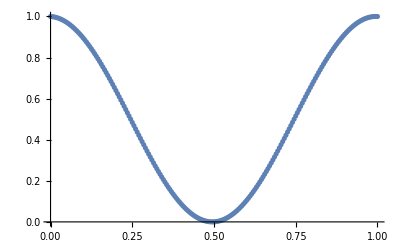

```mathematica
Ψ0=Transpose[{{1,0}}];
Ψk=Ψ0;
Δt=.005 ms;
list=Reap[Do[
k1=-I/ℏ H[t].Ψk;
k2 =-I/ℏ H[t+Δt/2].(Ψk+Δt/2 k1);
k3 =-I/ℏ H[t+Δt/2].(Ψk+Δt/2 k2);
k4 =-I/ℏ H[t+Δt].(Ψk+Δt k3);
Ψk=Ψk+ Δt/6(k1+2k2+2k3+k4);

Sow[{t/ms,Abs[Ψk[[1,1]]]^2,Abs[Ψk[[2,1]]]^2}];
,{t,0, 1ms,Δt}]][[2,1]];

ListPlot[list[[;;,{1,2}]]]
```